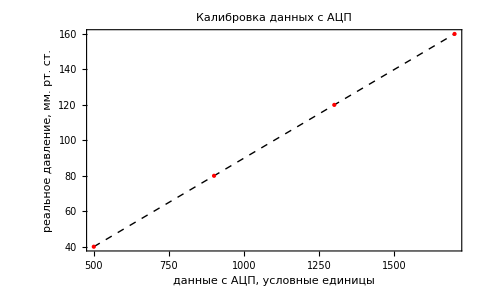

```mathematica
points={{500,40},{900,80},{1300,120},{1700,160}};
s =Show[Plot[0.1x-10,{x,500,1700},PlotStyle->{Dashed,Thin,Black}],ListPlot[points,PlotStyle->{Red,PointSize[Large]}],Frame->True,FrameLabel->{"данные с АЦП, условные единицы","реальное давление, мм. рт. ст."},PlotLabel->"Калибровка данных с АЦП"]
```

```mathematica
FindFit[points,a*x +b,{a,b},x]
```

{a→0.1,b→-10.}

```mathematica
time =Table[Import["C:\\Users\\SOFIA KANYUKOVA\\Desktop\\картинки в общеинженерку\\time.xlsx"]];
artpress = Table[Import["C:\\Users\\SOFIA KANYUKOVA\\Desktop\\картинки в общеинженерку\\artpress.xlsx"]];
```

```mathematica
ppp = Table[{time[[1]][[i]][[1]],artpress[[1]][[i]][[1]]},{i,2134}]
```

{{14.0002,108.8},{14.0105,108.5},{14.0209,108.4},{14.0312,108.3},{14.0415,108.1},{14.0518,108.},2123,{35.9491,7.4},{35.9594,7.3},{35.9697,7.3},{35.98,7.3},{35.9903,7.2}}
 |  |  |  |

```mathematica
FindFit[ppp, a*x^c +b,{a,b,c},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→-466.178,b→755.621,c→0.133719}

```mathematica
NonlinearModelFit[ppp,a*x^c+b,{a,b,c},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[755.621-466.178 x^0.133719]

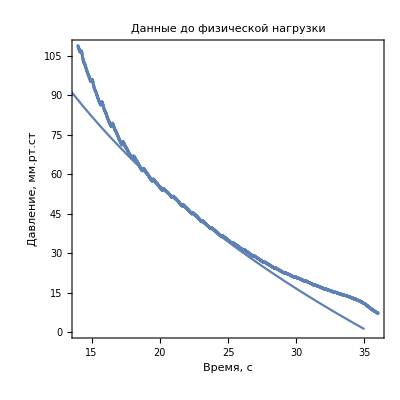

```mathematica
Show[ListPlot[ppp,Frame->True,AspectRatio->1,FrameLabel->{"Время, с", "Давление, мм.рт.ст"},PlotLabel->"Данные до физической нагрузки"],Plot[755.6212109223419-468.97767951447473 x^0.13371854566881392,{x,0,35}]]
```

```mathematica
pulse = Table[{time[[1]][[i]][[1]], artpress[[1]][[i]][[1]]-755.6212109223419-468.97767951447473 (time[[1]][[i]][[1]])^0.13371854566881392},{i,2134}]
```

{{14.0002,20.618},{14.0105,20.3837},{14.0209,20.3494},{14.0312,20.315},2127,{35.9697,8.87727},{35.98,8.90629},{35.9903,8.8353}}
 |  |  |  |

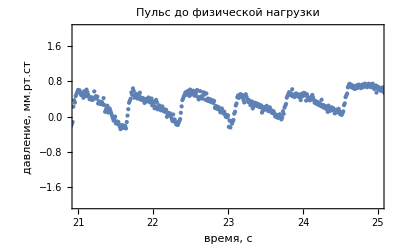

```mathematica
ListPlot[pulse,PlotStyle->PointSize[Medium],PlotRange->{{21,25},{-2,2}},Frame->True,FrameLabel->{"время, с","давление, мм.рт.ст"},PlotLabel->"Пульс до физической нагрузки"]
```

```mathematica
timeafter =Table[Import["C:\\Users\\SOFIA KANYUKOVA\\Desktop\\картинки в общеинженерку\\timeafter.xlsx"]];
artpressafter = Table[Import["C:\\Users\\SOFIA KANYUKOVA\\Desktop\\картинки в общеинженерку\\artpressafter.xlsx"]];
```

```mathematica
pppafter = Table[{timeafter[[1]][[i]][[1]],artpressafter[[1]][[i]][[1]]},{i,2136}];
```

```mathematica
NonlinearModelFit[pppafter,a*x^c+b,{a,b,c},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[904.757-525.025 x^0.146718]

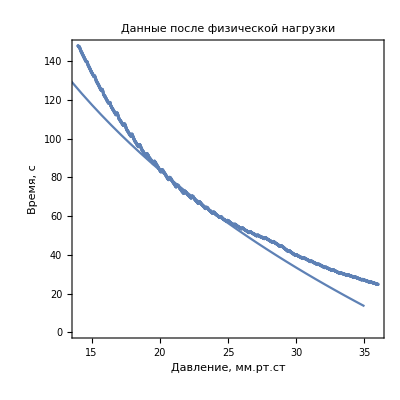

```mathematica
Show[ListPlot[pppafter,Frame->True,AspectRatio->1,FrameLabel->{"Давление, мм.рт.ст","Время, с"},PlotLabel->"Данные после физической нагрузки"],Plot[904.7567072434658-529.025486002589 x^0.14671802981540788,{x,0,35}]]
```

```mathematica
pulseafter=Table[{time[[1]][[i]][[1]],0.7+artpressafter[[1]][[i]][[1]] - (904.7567072434658-529.025486002589 * (time[[1]][[i]][[1]])^0.14671802981540788)},{i,2136}]
```

Part::partw: Part 2135 of {{14.0002},{14.0105},{14.0209},{14.0312},{14.0415},{14.0518},{14.0621},{14.0724},{14.0827},«33»,{14.4332},{14.4435},{14.4538},{14.4642},{14.4745},{14.4848},{14.4951},{14.5054},«2084»} does not exist.

Part::partw: Part 2136 of {{14.0002},{14.0105},{14.0209},{14.0312},{14.0415},{14.0518},{14.0621},{14.0724},{14.0827},«33»,{14.4332},{14.4435},{14.4538},{14.4642},{14.4745},{14.4848},{14.4951},{14.5054},«2084»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{14.0002,23.1188},2134,{{{14.0002},{14.0105},{14.0209},{14.0312},{14.0415},{14.0518},2122,{35.9387},{35.9491},{35.9594},{35.9697},{35.98},{35.9903}},1}}
 |  |  |  |

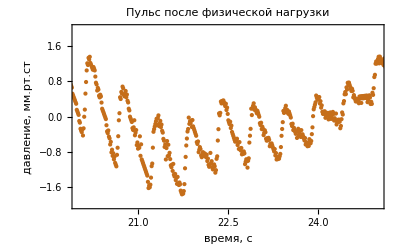

```mathematica
ListPlot[pulseafter,PlotRange->{{20,25},{-2,2}},Frame->True,FrameLabel->{"время, с","давление, мм.рт.ст"},PlotLabel->"Пульс после физической нагрузки",PlotStyle->PointSize[Medium]]
```

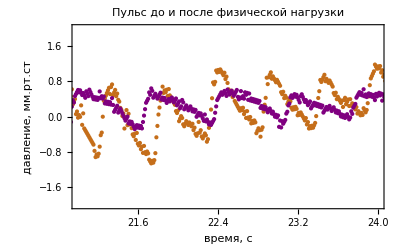

```mathematica
Show[ListPlot[pulseafter,PlotRange->{{21,24},{-2,2}},Frame->True,FrameLabel->{"время, с","давление, мм.рт.ст"},PlotLabel->"Пульс до и после физической нагрузки",PlotStyle->{Blue,PointSize[Medium]}],ListPlot[pulse,PlotStyle->{Purple,PointSize[Medium]},PlotRange->{{21,25},{-2,2}},Frame->True,FrameLabel->{"время, с","давление, мм.рт.ст"},PlotLabel->"Пульс до физической нагрузки"]]
```

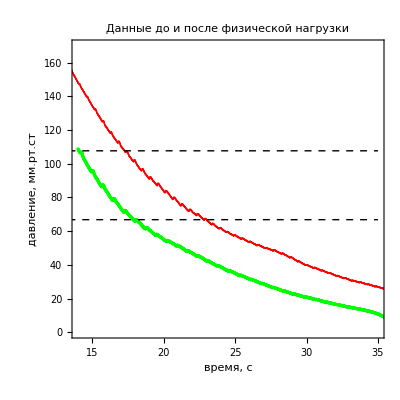

```mathematica
Show[ListPlot[ppp,Frame->True,PlotRange->{{14,35},{0,170}},AspectRatio->1,FrameLabel->{"время, с","давление, мм.рт.ст"},PlotLabel->"Данные до и после физической нагрузки",PlotStyle->Green],ListPlot[pppafter,Frame->True,AspectRatio->1,FrameLabel->{"давление, мм.рт.ст","время, с"},PlotLabel->"Данные после физической нагрузки",PlotStyle->Red],Plot[{107.66},{x,0,35},PlotStyle->{Black,Dashed,Thin}],Plot[{66.8},{x,0,35},PlotStyle->{Black,Dashed,Thin}]]
```